## prescribedPath1 : solve for prescribed path for 1st-order ODE Example 4.1

```mathematica
Clear["Global`*"]
```

```mathematica
xprescribed=t^n;
u=D[xprescribed, t]+ λ xprescribed
```

n t^(-1+n)+t^n λ

```mathematica
u/.{λ->1,n->{1,2}}
```

{1+t,2 t+t^2}

```mathematica
xsol=DSolveValue[{x'[t]+λ x[t]==u,x[0]==0},x[t],t,Assumptions->{λ>0,n>0}]//Simplify
```

t^n

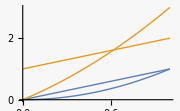

```mathematica
Plot[{xsol/.n->{1,2},u/.{λ->1,n->{1,2}}},{t,0,1}]
```